```mathematica
Units/definitions;
```

```mathematica
(*UNITS,
phonon Data read in in THz,
Converted to meV by 1THz=4.14meV,
Convert temperature from Kelvin to meV via 1K=8.6173324*10^-5eV,
2by2by2 supercell 64 atoms
*)
ClearAll
THz2meV = 4.14;
K2meV=0.086173324;
Natoms=64;
"alatts:"
alatts={4.575,4.685,4.730,4.759,4.801,4.850}
"temps:"
temps={0,760,1900,2500,3200,3805}
"Volumes:"
volumes=alatts^3
```

ClearAll

alatts:

{4.575,4.685,4.73,4.759,4.801,4.85}

temps:

{0,760,1900,2500,3200,3805}

Volumes:

{95.7576,102.832,105.824,107.782,110.661,114.084}

```mathematica
Quasiharmonic lattice free energy
```

energy free lattice Quasiharmonic

```mathematica
Import data Fqh data;  
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
fqhLatts={4.575,4.65837,4.725,4.800,4.875};
fqhVols=fqhLatts^3;
filesFqh={"Fqh_fromMeshfreq_4.575", "Fqh_fromMeshfreq_4.65837" ,"Fqh_fromMeshfreq_4.725" ,"Fqh_fromMeshfreq_4.800" ,"Fqh_fromMeshfreq_4.875"};
FqhData=Table[ReadList[filesFqh[[i]],{Number, Number}],{i,1,5}]
ListPlot[FqhData,AxesLabel->{"Temperature (K)","Fel\n (meV/atom)"},PlotLabel->"Quasiharmonic free energy",PlotRange->{{0,4000},{-2500,100}},Joined->True];
```

{{{0.,77.1884},{2.,77.1884},{4.,77.1884},{6.,77.1884},{8.,77.1883},{10.,77.1883},{12.,77.1882},{14.,77.1882},«1892»,{3800.,-1933.74},{3802.,-1935.28},{3804.,-1936.82},{3806.,-1938.35},{3808.,-1939.89},{3810.,-1941.43},{3812.,-1942.96},{3814.,-1944.5}},{«1»},«1»,{«1»},{«1»}}

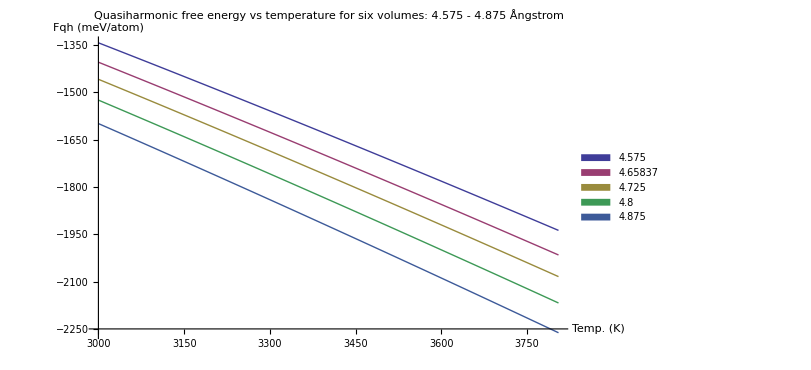

```mathematica
Harmonic Lattice Free Energy vs Volume;  
Plot[Evaluate@Table[Interpolation[FqhData[[i]]][temp],{i,1,5}],{temp,3000,3805},Axes->True,PlotLegends->Placed[SwatchLegend[{fqhLatts[[1]],fqhLatts[[2]],fqhLatts[[3]],fqhLatts[[4]],fqhLatts[[5]]}],{0.95,0.6}],ImageSize->600,AxesLabel->{"Temp. (K)","Fqh\n (meV/atom)"},PlotStyle->Thick,PlotRange->All,PlotLabel->"Quasiharmonic free energy vs temperature\n for six volumes: 4.575 - 4.875 Ångstrom"]
Fqh3805=Table[Interpolation[FqhData[[i]]][3805],{i,1,5}];
```

```mathematica
Harmonic Lattice Free Energy vs a latt;
```

```mathematica
(*Fqh as a function of temperature at five volumes*)
FqhTemp[temp_]:=Table[Interpolation[FqhData[[i]]][temp],{i,1,5}];
(*five temperatures*)
fqhtemps={760,1900,2500,3200,3805};
(*make a list of lattice parameters and free energy at temp 3805*)
Transpose[{fqhLatts,FqhTemp[3805]}];
(*Generalise by making a matrix at five temperatures, and pick out the 5th column (3805K)*)
Table[Table[FqhTemp[temp],{temp,{fqhtemps}}][[1,i]][[5]],{i,1,5}];
(*Tranpose the generalised version to get a (latts, Free energy at T) list*)
Transpose[{fqhLatts,Table[Table[FqhTemp[temp],{temp,{fqhtemps}}][[1,i]][[5]],{i,1,5}]}];
(*Interpolate, make a function of a, then plot*)
Plot[Interpolation[Transpose[{fqhLatts,Table[Table[FqhTemp[temp],{temp,{fqhtemps}}][[1,i]][[5]],{i,1,5}]}]][a],{a,4.575,4.875}];
(*Make a table of each free energy at each temperature as a function of a*)
FqhAlatt[a_]:=Table[Interpolation[Transpose[{fqhLatts,Table[Table[FqhTemp[temp],{temp,{fqhtemps}}][[1,i]][[j]],{i,1,5}]}]][a],{j,1,5}];
(*Plot*)
Plot[Evaluate@FqhAlatt[a],{a,4.575,4.875},AxesLabel->{"a (Å)","Fqh (meV/atom)"},
PlotLabel->"Lattice harmonic free energy vs volume \n for temperatures: 0 - 3800K",ImageSize->550,PlotStyle->Thick,PlotLegends->Placed[SwatchLegend[ Table[fqhtemps[[i]],{i,1,5}]],{1.0,0.6}],PlotRange->All]




(*Plot[Evaluate@Table[Interpolation[Transpose@{fqhLatts,Table[FqhTemp[temp],{temp,{fqhtemps}}][[1,i]]}][a],{i,1,5}],{a,4.575,4.875},AxesLabel->{"a (Å)","Fqh (meV/atom)"},
PlotLabel->"Lattice harmonic free energy vs volume \n for temperatures: 0 - 3800K",ImageSize->550,PlotStyle->Thick,PlotLegends->Placed[SwatchLegend[ Table[fqhtemps[[i]],{i,1,5}]],{0.95,0.6}],PlotRange->All]*)
(*Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}]};
Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,1]]},{i,1,9}];
Table[Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]}][volume],{i,1,9}]
Plot[Table[Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]}][volume],{i,1,9}],{volume,felLatts[[1]],felLatts[[9]]}]*)
```

-Graphics-

```mathematica
Harmonic Lattice Gruneisen vs Volume;
```

(a InterpolatingFunction[{{4.575,4.875}},<>][a]')/(InterpolatingFunction[{{4.575,4.875}},<>][a])

InterpolatingFunction::dmval: Input value {4.50001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

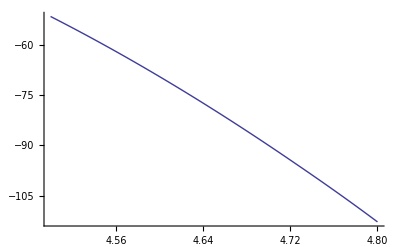

-Graphics-

```mathematica
Off[Part::pspec,Transpose::nmtx,Interpolation::innd]
FqhTemp[temp_]:=Table[Interpolation[FqhData[[i]]][temp],{i,1,5}];
fqhtemps={760,1900,2500,3200,3805};
harmonicEnergy[vol_]:=Interpolation[Transpose@{fqhVols,Table[FqhTemp[temp],{temp,{fqhtemps}}][[1,i]]}][vol]
grun=Evaluate[a/FqhAlatt[a][[1]]*(FqhAlatt[a][[1]]')]
Plot[(FqhAlatt[a][[1]]),{a,4.5,4.8}]
Plot[grun,{a,fqhLatts[[1]],fqhLatts[[5]]},AxesLabel->{"a latt (Å)","Gruneisen"},
PlotLabel->"Gruneisen parameter vs volume\n for temperatures: 0 - 3800K",ImageSize->550,PlotStyle->Thick,PlotLegends->Placed[SwatchLegend[ Table[fqhtemps[[i]],{i,1,5}]],{0.95,0.6}],PlotRange->All]
(*
{{-10,20},{90,120}}
Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}]};
Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,1]]},{i,1,9}];
Table[Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]}][volume],{i,1,9}]
Plot[Table[Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]}][volume],{i,1,9}],{volume,felLatts[[1]],felLatts[[9]]}]*)
```

```mathematica
Anharmonic lattice free energy
```

Anharmonic energy free lattice

```mathematica
Import data Fah data;
```

```mathematica
(*Fah data given from V1 (smallest volume) to V2 Largest volume, from smallest to largest temperature*)
FahV0={0,0,0,0,0,0};
FahV1={0,-1.82440022718568,-2.96042804411382,-4.88492907279111,-6.74390310049199,-10.8865661622225};
FahV2={0,-1.12373671674498,-1.80953812696422,-3.06094004561156,-3.93420405862421,-7.63112711371265};
FahV3={0,-0.744224011089802,-0.32745500487946,-0.251783003751859,-2.14531003196761,-3.8};
FahV4={0,-0.755542011258453,1.18097901759796,1.77304902642049,1.68729402514264,3.32610804956287};
FahV5={0,-0.402489005997553,4.78285607127011,6.67826609951392,10.7690871604719,13.6921642040291};
filesFah={FahV0,FahV1,FahV2,FahV3,FahV4,FahV5};
```

```mathematica
(*Andy data*)
FahV0A={0,0,0,0,0,0};
FahV1A={0,-0.250215,-0.1621077,-0.02198894,-0.172075,-1.6195515};
FahV2A={0,0.544,1.454731,2.5837645,2.719392,1.160370};
FahV3A={0,0.934165,3.8724,5.0497218,5.650589,6.111593};
FahV4A={0,1.47966,5.74540751,7.7660415,10.236911,11.4962796};
FahV5A={0,1.98531,8.684873,12.195615,18.74885,20.58148597};
filesFahA={FahV0A,FahV1A,FahV2A,FahV3A,FahV4A,FahV5A};
```

```mathematica
Anharmonic Free Energy vs Temperature;
```

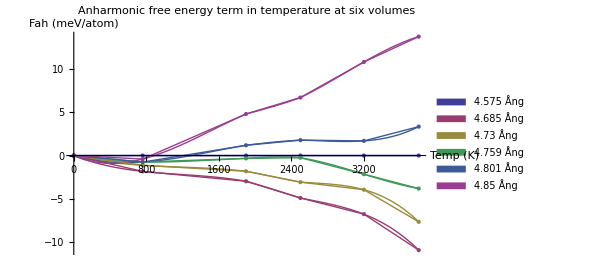

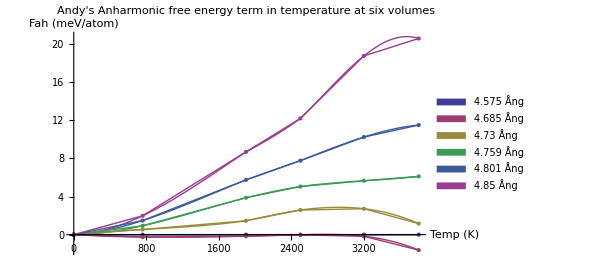

```mathematica
Show[Plot[Evaluate@Table[Interpolation[Transpose@{temps,filesFah[[i]]}][test],{i,1,6}],{test,0,3805},AxesLabel->{"Temp (K)","Fah (meV/atom)"},PlotLabel->"Anharmonic free energy term in temperature\n at six volumes",ImageSize->450,PlotStyle->Thick,PlotRange->All,PlotLegends->Placed[SwatchLegend[{alatts[[1]]Ång,alatts[[2]]Ång,alatts[[3]]Ång,alatts[[4]]Ång,alatts[[5]]Ång,alatts[[6]]Ång}],{0.14,0.74}]],ListPlot[Table[Transpose@{temps,filesFah[[i]]},{i,1,6}],Joined->True],ListPlot[Table[Transpose@{temps,filesFah[[i]]},{i,1,6}]]
]
Show[Plot[Evaluate@Table[Interpolation[Transpose@{temps,filesFahA[[i]]}][test],{i,1,6}],{test,0,3805},AxesLabel->{"Temp (K)","Fah (meV/atom)"},PlotLabel->"Andy's Anharmonic free energy term in temperature\n at six volumes",ImageSize->450,PlotStyle->Thick,PlotRange->All,PlotLegends->Placed[SwatchLegend[{alatts[[1]]Ång,alatts[[2]]Ång,alatts[[3]]Ång,alatts[[4]]Ång,alatts[[5]]Ång,alatts[[6]]Ång}],{0.15,0.6}]],ListPlot[Table[Transpose@{temps,filesFahA[[i]]},{i,1,6}],Joined->True],ListPlot[Table[Transpose@{temps,filesFahA[[i]]},{i,1,6}]]
]
```

```mathematica
Anharmonic Free Energy vs Volume;
```

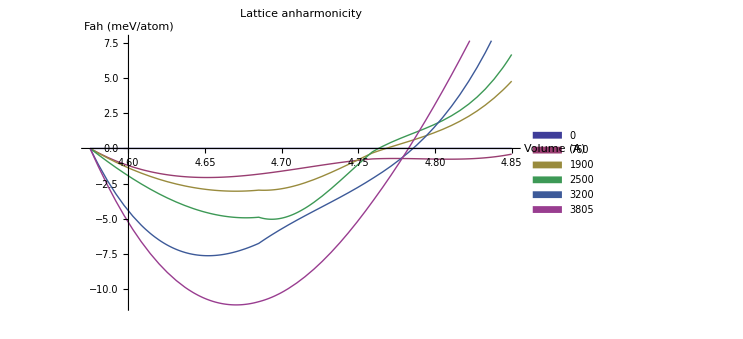

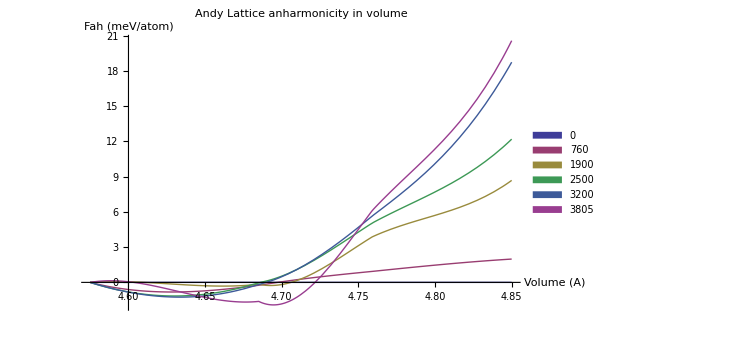

```mathematica
(*Show the Free energy shape vs volume*)

FahVol=Evaluate@Table[Interpolation[Transpose@{alatts,Transpose[filesFah][[i]]}][vol],{i,1,6}];
Show[Plot[Evaluate@Table[Interpolation[Transpose@{alatts,Transpose[filesFah][[i]]}][vol],{i,1,6}],{vol,4.575,4.85},AxesLabel->{"Volume (A)","Fah (meV/atom)"},PlotLabel->"Lattice anharmonicity",ImageSize->550,PlotStyle->Thick,PlotLegends->Placed[SwatchLegend[{temps[[1]],temps[[2]],temps[[3]],temps[[4]],temps[[5]],temps[[6]]}],{0.25,0.8}]],PlotRange->All]
Show[Plot[Evaluate@Table[Interpolation[Transpose@{alatts,Transpose[filesFahA][[i]]}][vol],{i,1,6}],{vol,4.575,4.85},AxesLabel->{"Volume (A)","Fah (meV/atom)"},PlotLabel->"Andy Lattice anharmonicity in volume",ImageSize->550,PlotStyle->Thick,PlotLegends->Placed[SwatchLegend[{temps[[1]],temps[[2]],temps[[3]],temps[[4]],temps[[5]],temps[[6]]}],{0.25,0.8}]],PlotRange->All]
```

```mathematica
Electronic free energy
```

Electronic energy free

```mathematica
Import data Fel data;  
Off[InterpolatingFunction::dmval,General::stop]
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Zr_Fel"];
felLatts={4.658,4.675,4.700,4.725,4.750,4.775,4.800,4.825,4.850,4.875};
filesFel={"Fel_4.658Ang","Fel_4.675Ang","Fel_4.7Ang","Fel_4.725Ang", "Fel_4.75Ang","Fel_4.775Ang","Fel_4.8Ang" ,"Fel_4.825Ang" ,"Fel_4.85Ang" ,"Fel_4.875Ang"};
FelData=Table[ReadList[filesFel[[i]],{Number, Number}],{i,1,10}];
ListPlot[FelData,AxesLabel->{"Temperature (K)","Fel\n (meV/atom)"},PlotLabel->"Electronic free energy"];
```

```mathematica
Electronic Free Energy vs Temperature;
```

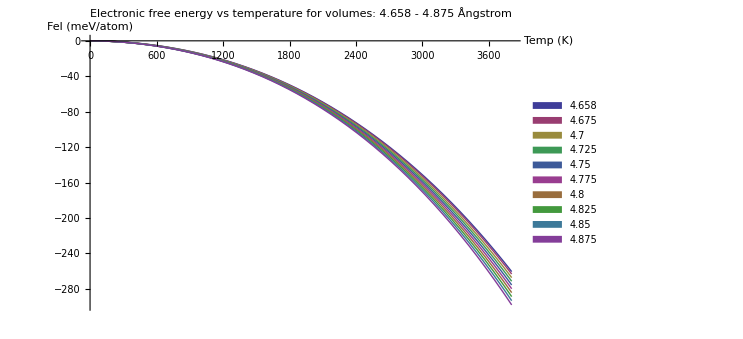

```mathematica
Plot[Evaluate@Table[Interpolation[FelData[[i]]][temp],{i,1,10}],{temp,1,3805},PlotLegends->Placed[SwatchLegend[{felLatts[[1]],felLatts[[2]],felLatts[[3]],felLatts[[4]],felLatts[[5]],felLatts[[6]],felLatts[[7]],felLatts[[8]],felLatts[[9]],felLatts[[10]]}],{0.95,0.6}],ImageSize->550,AxesLabel->{"Temp (K)","Fel\n (meV/atom)"},PlotLabel->"Electronic free energy vs temperature\n for volumes: 4.658 - 4.875 Ångstrom",Axes->True,PlotStyle->Thick]
```

```mathematica
Electronic Free Energy vs Volume;
```

```mathematica
felVolume[volume_]:=Table[Interpolation[Transpose@{felLatts,FelTemp[temp]}][volume],{temp,{feltemps}}]
Plot[{felVolume[volume]},{volume,felLatts[[1]],felLatts[[10]]},AxesLabel->{"Volume (A^3)","Fel (meV/atom)"},PlotLabel->"Electronic free energy vs volume\n for temperatures: 0 - 3800K",ImageSize->550,PlotStyle->Thick,PlotLegends->SwatchLegend[ Table[feltemps[[i]],{i,1,10}]],PlotRange->{{4.65,4.85},{0,-300}}]
```

Part::partd: Part specification feltemps ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 4 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 5 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 6 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 8 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 9 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 10 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 4 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 5 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 6 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 8 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 9 ⟧ is longer than depth of object.

Part::partd: Part specification feltemps ⟦ 10 ⟧ is longer than depth of object.

-Graphics-

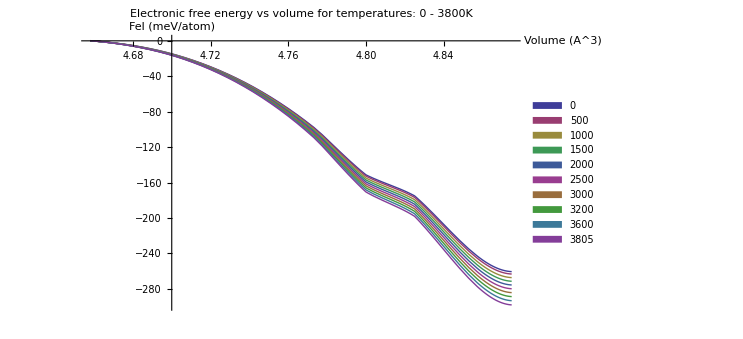

```mathematica
FelTemp[temp_]:=Table[Interpolation[FelData[[i]]][temp],{i,1,10}];
Felfiles=Transpose@{FelTemp[0],FelTemp[500],FelTemp[1000],FelTemp[1500],FelTemp[2000],FelTemp[2500],FelTemp[3000],FelTemp[3200],FelTemp[3600],FelTemp[3805]};
feltemps={0,500,1000,1500,2000,2500,3000,3200,3600,3805};
Plot[Evaluate@Table[Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]}][volume],{i,1,10}],{volume,4.658,4.875},AxesLabel->{"Volume (A^3)","Fel (meV/atom)"},PlotLabel->"Electronic free energy vs volume\n for temperatures: 0 - 3800K",ImageSize->550,PlotStyle->Thick,PlotLegends->SwatchLegend[ Table[feltemps[[i]],{i,1,10}]],PlotRange->All]
(*Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}]};
Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,1]]},{i,1,9}];
Table[Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]}][volume],{i,1,9}]
Plot[Table[Interpolation[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]}][volume],{i,1,9}],{volume,felLatts[[1]],felLatts[[9]]}]*)
```

```mathematica
Table[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]},{i,1,10}]
ListPlot[Table[Transpose@{felLatts,Table[FelTemp[temp],{temp,{feltemps}}][[1,i]]},{i,1,10}]];
```

{{{4.658,0.0892015},{4.675,-3.64151},{4.7,-14.6351},{4.725,-33.835},{4.75,-62.2384},{4.775,-100.947},{4.8,-151.239},{4.825,-174.93},{4.85,-229.028},{4.875,-260.456}},{{4.658,0.109656},{4.675,-3.71377},{4.7,-14.8089},{4.725,-34.1642},{4.75,-62.8109},{4.775,-101.88},{4.8,-152.688},{4.825,-176.638},{4.85,-231.357},{4.875,-263.161}},{{4.658,0.138678},{4.675,-3.82223},{4.7,-15.0631},{4.725,-34.6457},{4.75,-63.6512},{4.775,-103.258},{4.8,-154.842},{4.825,-179.182},{4.85,-234.836},{4.875,-267.208}},{{4.658,0.157236},{4.675,-3.91796},{4.7,-15.2992},{4.725,-35.1082},{4.75,-64.4756},{4.775,-104.632},{4.8,-157.011},{4.825,-181.752},{4.85,-238.372},{4.875,-271.328}},{{4.658,0.166746},{4.675,-3.98765},{4.7,-15.5053},{4.725,-35.5392},{4.75,-65.2728},{4.775,-105.991},{4.8,-159.188},{4.825,-184.342},{4.85,-241.956},{4.875,-275.518}},{{4.658,0.169848},{4.675,-4.03855},{4.7,-15.6873},{4.725,-35.9461},{4.75,-66.0515},{4.775,-107.345},{4.8,-161.382},{4.825,-186.962},{4.85,-245.604},{4.875,-279.789}},{{4.658,0.171186},{4.675,-4.08587},{4.7,-15.8607},{4.725,-36.3449},{4.75,-66.8278},{4.775,-108.71},{4.8,-163.615},{4.825,-189.634},{4.85,-249.336},{4.875,-284.167}},{{4.658,0.170799},{4.675,-4.12765},{4.7,-16.0244},{4.725,-36.7346},{4.75,-67.6042},{4.775,-110.092},{4.8,-165.889},{4.825,-192.364},{4.85,-253.163},{4.875,-288.661}},{{4.658,0.163393},{4.675,-4.15706},{4.7,-16.1728},{4.725,-37.1126},{4.75,-68.3762},{4.775,-111.486},{4.8,-168.208},{4.825,-195.151},{4.85,-257.084},{4.875,-293.273}},{{4.658,0.15118},{4.675,-4.17565},{4.7,-16.3096},{4.725,-37.481},{4.75,-69.1485},{4.775,-112.901},{4.8,-170.576},{4.825,-198.006},{4.85,-261.113},{4.875,-298.016}}}

```mathematica
U0 vs Volume;
```

{766.061,808.516,843.909,884.736,926.859}

{-673.839,-675.71,-674.609,-670.996,-665.213}

{4.575,4.658,4.725,4.8,4.875}

{29.2285,0.,17.2066,73.6594,164.017}

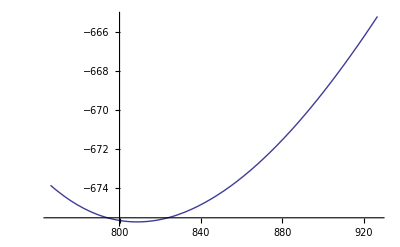

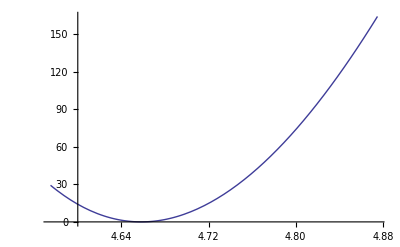

```mathematica
U0vol={766.060875,808.515666496,843.908625,884.7360000,926.85937500}
U0energy={-673.839280,-675.709904,-674.608680,-670.995704,-665.212792}
vol2latt[vol_]:=0.5*(vol^(1/3))
U0latt=vol2latt[U0vol]
super2meVatomRel[cell_]:=(1000/64)*(cell-cell[[2]])
U0energymeVatom=super2meVatomRel[U0energy]
Plot[Interpolation[Transpose@{U0vol,U0energy}][a],{a,U0vol[[1]],U0vol[[5]]}]
Plot[Interpolation[Transpose@{U0latt,U0energymeVatom}][a],{a,U0latt[[1]],U0latt[[5]]}]
```

```mathematica
{766.060875,808.515666496,843.908625,884.736,26.859375}
```

{766.061,808.516,843.909,884.736,26.8594}

```mathematica
Total Free Energy vs Volume at 3805K;
```

```mathematica
U03805rel[volume_]:=Interpolation[Transpose@{U0latt,U0energymeVatom}][volume]
Fel3805[volume_]:=Interpolation[Transpose@{felLatts,FelTemp[3805]}][volume]
Fel3805rel[volume_]:=(Interpolation[Transpose@{felLatts,FelTemp[3805]}][volume]-Interpolation[Transpose@{felLatts,FelTemp[3805]}][4.65])
fqh3805[volume_]:=Evaluate@(FqhAlatt[volume])[[5]]
Fqh3805rel[volume_]:=Evaluate@(FqhAlatt[volume]-FqhAlatt[4.65])[[5]]
Fah3805[volume_]:=Evaluate@Table[Interpolation[Transpose@{alatts,Transpose[filesFahA][[i]]}][volume],{i,5,5}]

Fah3805rel[volume_]:=Evaluate@Table[(Interpolation[Transpose@{alatts,Transpose[filesFahA][[i]]}][volume]-Interpolation[Transpose@{alatts,Transpose[filesFahA][[i]]}][4.65]),{i,5,5}]

(*Plot[Interpolation[Transpose@{felLatts,FelTemp[3805]}][volume]+Evaluate@Table[Interpolation[Transpose@{alatts,Transpose[filesFahA][[i]]}][volume],{i,5,5}]+Evaluate@FqhAlatt[volume][[5]],{volume,4.65,4.85}]
Plot[Evaluate@FqhAlatt[a][[5]],{a,4.575,4.875},AxesLabel->{"a (Å)","Fqh (meV/atom)"},
PlotLabel->"Lattice harmonic free energy vs volume \n for temperatures: 0 - 3800K",ImageSize->550,PlotStyle->Thick,PlotLegends->Placed[SwatchLegend[ Table[fqhtemps[[i]],{i,1,5}]],{1.0,0.6}],PlotRange->All]*)
```

```mathematica
u0rel=Plot[U03805rel[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.1]},PlotLegends->SwatchLegend[{"Zero T crystal"}]];
fel=Plot[Fel3805[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.3]},PlotLegends->SwatchLegend[{"Electrons"}]];
felrel=Plot[Fel3805rel[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.3]},PlotLegends->SwatchLegend[{"Electrons"}]];
fqh=Plot[fqh3805[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.5]},PlotLegends->SwatchLegend[{"Quasiharmonic phonons"}]];
fqhrel=Plot[Fqh3805rel[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.5]},PlotLegends->SwatchLegend[{"Quasiharmonic phonons"}]];
fah=Plot[Fah3805[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.8]},PlotLegends->SwatchLegend[{"Anharmnonic phonons"}]];
fahrel=Plot[Fah3805rel[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.8]},PlotLegends->SwatchLegend[{"Anharmnonic phonons"}]];

sumrel=Plot[U03805rel[volume]+Fel3805rel[volume]+Fqh3805rel[volume]+Fah3805rel[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.0]},PlotLegends->SwatchLegend[{"Total free energy"}]];
sum=Plot[U03805rel[volume]+Fel3805[volume]+fqh3805[volume]+Fah3805[volume],{volume,4.65,4.85},PlotStyle->{Thick,Hue[0.0]},PlotLegends->SwatchLegend[{"Total free energy"}]];
Show[u0rel,fel,fqh,fah,sum,PlotRange->All];
```

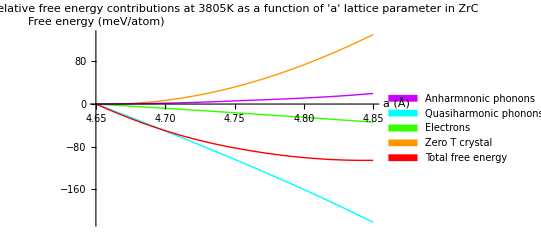

```mathematica
Show[u0rel,felrel,fqhrel,fahrel,sumrel,PlotRange->All,PlotLabel->"Relative free energy contributions at 3805K \n as a function of 'a' lattice parameter in ZrC",AxesLabel->{"a (Å)","Free energy (meV/atom)"}]
```